# Робилко Т . М . 221701 Лабораторная Работа 3 - Интерполяция и среднеквадратичное приближение

```mathematica
f[x_]=(Sinh[√(x^2+x+5)]+π)/(√(3 x^8+11 x^4+33)); (* Вариант 10 *)
```

### Задание 1 (n = 6)

```mathematica
A=0;
B=6;
n=6;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 1.35195
1. | 1.48099
2. | 0.540904
3. | 0.236911
4. | 0.173183
5. | 0.173726
6. | 0.212533

```mathematica
dataX=data[[All,1]];
dataY=data[[All,2]];
```

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*∏_(j=1)^n If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1];
```

```mathematica
Ln=LagrangeInterpolation[dataX,dataY,n+1]//Simplify;
Print["Ln(x)=", Ln];
```

Ln(x)=1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6

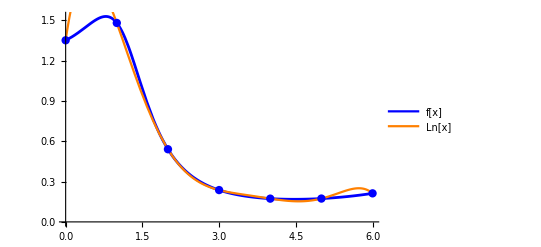

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Ln[x]"}]]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]=0]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

1.35195 | 0.129032 | -1.06911 | 1.7052 | -2.10103 | 2.32086 | -2.39069
1.48099 | -0.940083 | 0.63609 | -0.395824 | 0.219828 | -0.0698367 | 0
0.540904 | -0.303993 | 0.240266 | -0.175996 | 0.149991 | 0 | 0
0.236911 | -0.0637272 | 0.0642698 | -0.0260053 | 0 | 0 | 0
0.173183 | 0.000542657 | 0.0382646 | 0 | 0 | 0 | 0
0.173726 | 0.0388072 | 0 | 0 | 0 | 0 | 0
0.212533 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
NewtonInterpolationMultiplier[dataX_,n_,i_,H_]:=(∏_(k=1)^i ((x-dataX[[n]])/H+k-1))/(i!)
NewtonInterpolationSecondMethod[dataX_,dataY_,deltaTable_,H_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) (NewtonInterpolationMultiplier[dataX,n,i,H]*deltaTable[[n-i,i+1]]);
```

```mathematica
Pn=NewtonInterpolationSecondMethod[dataX,dataY,tableData,H,n+1]//Simplify;
Print["Pn(x)="Newton];
```

Pn(x)= (1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6)

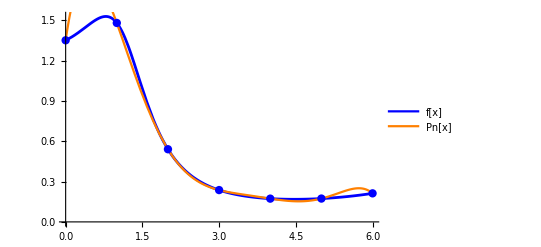

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Pn,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Pn[x]"}]]
```

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np];
Print["Np(x)=",Np];
```

Np(x)=1.35195+2.61987 x-4.22694 x^2+2.23346 x^3-0.563182 x^4+0.0691465 x^5-0.00332041 x^6

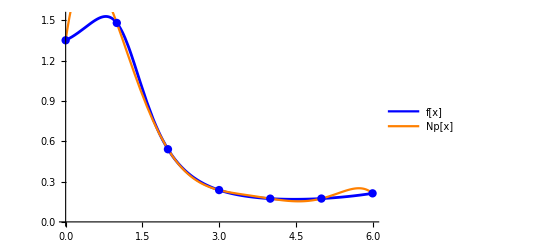

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Np,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Np[x]"}]]
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Ln[2.4316]= ",Ln/.x->2.4316];
Print["Pn[2.4316]= ",Pn/.x->2.4316];
Print["Np[2.4316]= ",Np/.x->2.4316];
```

f[2.4316]= 0.350875

Ln[2.4316]= 0.343952

Pn[2.4316]= 0.343952

Np[2.4316]= 0.343952

```mathematica
Rn=Abs[f[x]-Np];
```

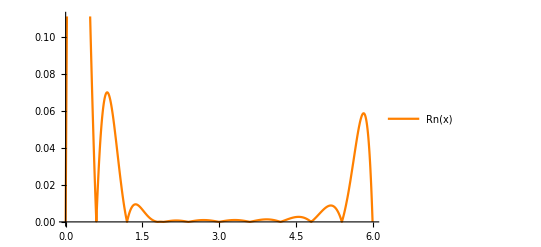

```mathematica
func1=Plot[Rn,{x,0,6},PlotStyle->Orange];
Legended[Show[func1],LineLegend[{Orange},{"Rn(x)"}]]
```

```mathematica
FindMaximum[{Rn,A<=x<=B},x] (* Тут задание 1 Е *)
```

{0.402046,{x→.372542680323273`}}

### Задание 1 (n = 10)

```mathematica
n=10;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 1.35195
0.6 | 1.50591
1.2 | 1.33212
1.8 | 0.685663
2.4 | 0.360695
3. | 0.236911
3.6 | 0.187258
4.2 | 0.169776
4.8 | 0.170404
5.4 | 0.184714
6. | 0.212533

```mathematica
dataX=data[[All,1]];
dataY=data[[All,2]];
```

```mathematica
Ln=LagrangeInterpolation[dataX,dataY,n+1]//Simplify;
Print["Ln(x)=",Ln];
```

Ln(x)=1.35195-4.76894 x+21.1867 x^2-34.0133 x^3+27.9651 x^4-13.7075 x^5+4.2577 x^6-0.84853 x^7+0.105364 x^8-0.00742946 x^9+0.000227331 x^10

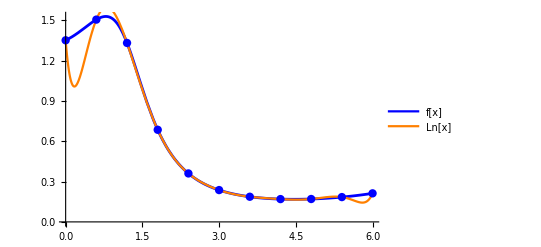

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Ln[x]"}]]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData, Frame->All]
```

1.35195 | 0.153951 | -0.327734 | -0.144945 | 0.939116 | -1.8536 | 2.76133 | -3.57724 | 4.24413 | -4.72309 | 4.98809
1.50591 | -0.173782 | -0.472678 | 0.794171 | -0.91448 | 0.907738 | -0.815906 | 0.666889 | -0.478957 | 0.265007 | 0
1.33212 | -0.646461 | 0.321493 | -0.120309 | -0.00674231 | 0.0918314 | -0.149017 | 0.187932 | -0.21395 | 0 | 0
0.685663 | -0.324968 | 0.201184 | -0.127051 | 0.0850891 | -0.057186 | 0.0389142 | -0.0260184 | 0 | 0 | 0
0.360695 | -0.123784 | 0.0741321 | -0.0419624 | 0.027903 | -0.0182718 | 0.0128958 | 0 | 0 | 0 | 0
0.236911 | -0.0496523 | 0.0321697 | -0.0140594 | 0.00963124 | -0.00537599 | 0 | 0 | 0 | 0 | 0
0.187258 | -0.0174825 | 0.0181104 | -0.00442811 | 0.00425525 | 0 | 0 | 0 | 0 | 0 | 0
0.169776 | 0.000627854 | 0.0136823 | -0.000172862 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.170404 | 0.0143101 | 0.0135094 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.184714 | 0.0278195 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.212533 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Pn=NewtonInterpolationSecondMethod[dataX,dataY,tableData,H,n+1]//Simplify;
Print["Pn(x)=",Pn];
```

Pn(x)=1.35195-4.76894 x+21.1867 x^2-34.0133 x^3+27.9651 x^4-13.7075 x^5+4.2577 x^6-0.84853 x^7+0.105364 x^8-0.00742946 x^9+0.000227331 x^10

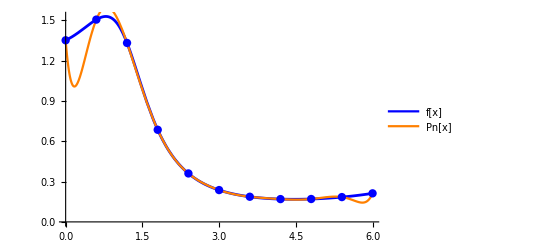

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Pn,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Pn[x]"}]]
```

```mathematica
Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np];
Print["Np(x)=",Np];
```

Np(x)=1.35195-4.76894 x+21.1867 x^2-34.0133 x^3+27.9651 x^4-13.7075 x^5+4.2577 x^6-0.84853 x^7+0.105364 x^8-0.00742946 x^9+0.000227331 x^10

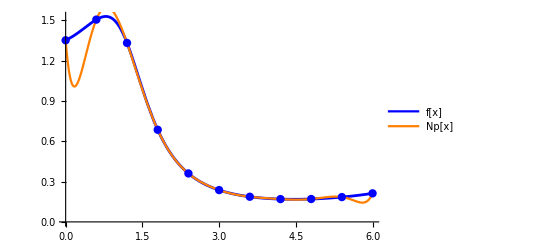

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Np,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Np[x]"}]]
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print[ "Ln[2.4316]= ",Ln/.x->2.4316];
Print[ "Pn[2.4316]= ",Pn/.x->2.4316];
Print["Np[2.4316]= ",Np/.x->2.4316];
```

f[2.4316]= 0.350875

Ln[2.4316]= 0.351038

Pn[2.4316]= 0.351038

Np[2.4316]= 0.351038

```mathematica
Rn=Abs[f[x]-Np];
```

```mathematica
func1=Plot[Rn,{x,0,6},PlotStyle->Orange];
Legended[Show[func1],LineLegend[{Orange},{"Rn(x)"}]]
```

-Graphics-

```mathematica
FindMaximum[{Rn,A<=x<=B},{x,0}]
```

{0.383245,{x→0.187989}}

### Задание 2 (n = 6)

```mathematica
n=6;
```

```mathematica
For[i=0,i<=n,i++,
Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(A+B)/2+(B-A)/2*Subscript[t, i];]
```

```mathematica
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

5.92478 | 0.208242
5.34549 | 0.182875
4.30165 | 0.168805
3. | 0.236911
1.69835 | 0.777439
0.654506 | 1.5168
0.0752163 | 1.36691

```mathematica
DividedDifferenceRecursive[dataX_,dataY_,begin_,end_]:=If[begin+1==end,(dataY[[end]]-dataY[[begin]])/(dataX[[end]]-dataX[[begin]]),(DividedDifferenceRecursive[dataX,dataY,begin+1,end]-DividedDifferenceRecursive[dataX,dataY,begin,end-1])/(dataX[[end]]-dataX[[begin]])]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,	For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=DividedDifferenceRecursive[dataX,dataY,i+1,k+i+1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

0.208242 | 0.0437901 | 0.0186745 | -0.00320707 | 0.00646566 | 0.00262241 | -0.00117389
0.182875 | 0.0134789 | 0.0280544 | -0.0305338 | -0.00735518 | 0.00948917 | 0
0.168805 | -0.0523226 | 0.139416 | 0.0039693 | -0.0573657 | 0 | 0
0.236911 | -0.415264 | 0.124939 | 0.246422 | 0 | 0 | 0
0.777439 | -0.708307 | -0.595792 | 0 | 0 | 0 | 0
1.5168 | 0.258742 | 0 | 0 | 0 | 0 | 0
1.36691 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
differenceResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
NewtonDivDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=NewtonDivDiff[dataX,dataY,n,differenceResult]//Simplify;
Print["Pnr(x)=",Pnr];
```

Pnr(x)=1.26612+1.51061 x-2.34974 x^2+1.10896 x^3-0.24822 x^4+0.0271858 x^5-0.00117389 x^6

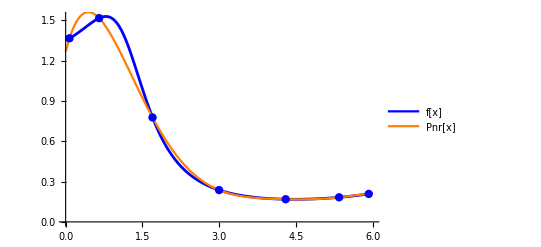

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Pnr,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Pnr[x]"}]]
```

```mathematica
Intf = Interpolation[data];
```

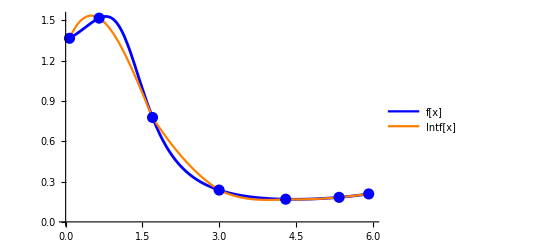

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Intf[x],{x,dataX[[n+1]],B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Intf[x]"}]]
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print[ "Pnr[2.4316]= ",Pnr/.x->2.4316];
Print["Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 0.350875

Pnr[2.4316]= 0.380613

Intf[2.4316]= 0.417935

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
FindMaximum[{AbsPnr[x],A<=x<=B},x]
```

{0.113657,{x→0.330325}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
FindMaximum[{AbsIntf[x],A<=x<=B},x]
```

{0.0779474,{x→0.338156}}

### Задание 2 (n = 10)

```mathematica
n=10;
```

```mathematica
For[i=0,i<=n,i++,
Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(A+B)/2+(B-A)/2*Subscript[t, i]]
```

```mathematica
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

5.96946 | 0.210762
5.7289 | 0.198185
5.26725 | 0.180425
4.62192 | 0.168696
3.8452 | 0.177356
3. | 0.236911
2.1548 | 0.456838
1.37808 | 1.13487
0.732751 | 1.5271
0.271104 | 1.41546
0.0305357 | 1.35776

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=DividedDifferenceRecursive[dataX,dataY,i+1,k+i+1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

0.210762 | 0.0522787 | 0.0196623 | 0.000984804 | 0.00103476 | -0.000369922 | 0.000303657 | -0.0000649449 | -0.000370011 | -0.000272437 | -0.0000850628
0.198185 | 0.0384715 | 0.0183353 | -0.0012133 | 0.00213323 | -0.00152827 | 0.000601844 | 0.0018727 | 0.00118243 | 0.000232745 | 0
0.180425 | 0.0181748 | 0.0206208 | -0.00703466 | 0.00759542 | -0.00414679 | -0.00875442 | -0.00458079 | -0.000143828 | 0 | 0
0.168696 | -0.011149 | 0.0365701 | -0.030675 | 0.023723 | 0.0355501 | 0.0141319 | -0.0038276 | 0 | 0 | 0
0.177356 | -0.0704628 | 0.112249 | -0.107629 | -0.114537 | -0.025935 | 0.0317059 | 0 | 0 | 0 | 0
0.236911 | -0.260208 | 0.377782 | 0.248863 | -0.0218431 | -0.146882 | 0 | 0 | 0 | 0 | 0
0.456838 | -0.872941 | -0.186452 | 0.308471 | 0.414318 | 0 | 0 | 0 | 0 | 0 | 0
1.13487 | -0.607797 | -0.767518 | -0.571652 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.5271 | 0.241825 | 0.00280749 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.41546 | 0.239853 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.35776 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
differenceResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
Pnr=NewtonDivDiff[dataX,dataY,n,differenceResult]//Simplify;
Print["Pnr(x)=",Pnr];
```

Pnr(x)=1.35877-0.0759415 x+1.45207 x^2-1.34812 x^3-0.82115 x^4+1.46293 x^5-0.766402 x^6+0.207231 x^7-0.0313769 x^8+0.00253204 x^9-0.0000850628 x^10

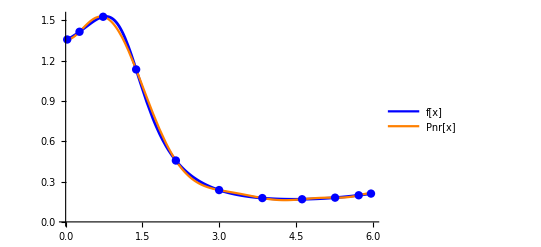

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Pnr,{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.015],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Pnr[x]"}]]
```

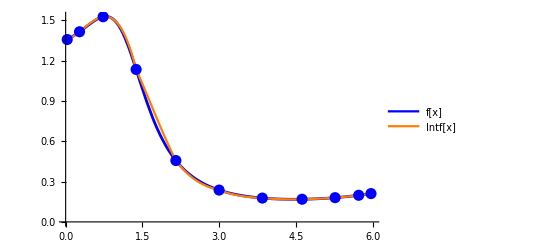

```mathematica
Intf=Interpolation[data];
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Intf[x],{x,dataX[[n+1]],B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Intf[x]"}]]
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Pnr[2.4316]= ",Pnr/.x->2.4316];
Print[ "Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 0.350875

Pnr[2.4316]= 0.332651

Intf[2.4316]= 0.343216

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
FindMaximum[{AbsPnr[x],A<=x<=B},{x,0.1}]
```

{0.00890886,{x→0.134523}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
FindMaximum[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},{x,3.4}]
```

#### Вывод : Как показали результаты, увеличение количества узлов позволяет уменьшить погрешность интерполирования. При этом неравномерное распределение узлов (оптимальный выбор их расположения) по отрезку позволяет уменьшить погрешность, в частности вблизи крайних участков отрезка.

### Задание 4

{0.00350652,{x→3.38986}}

```mathematica
n=10;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 1.35195
0.6 | 1.50591
1.2 | 1.33212
1.8 | 0.685663
2.4 | 0.360695
3. | 0.236911
3.6 | 0.187258
4.2 | 0.169776
4.8 | 0.170404
5.4 | 0.184714
6. | 0.212533

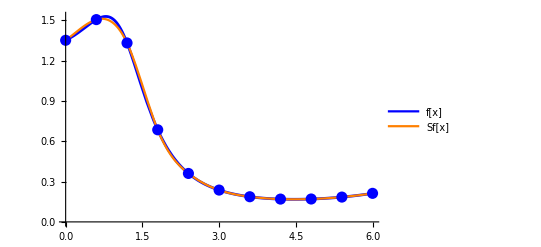

```mathematica
Sf=Interpolation[data,Method->"Spline"];
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Sf[x],{x,dataX[[n+1]],B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Sf[x]"}]]
```

```mathematica
Print["f[2.4316]= ",f[2.4316]];
Print["Sf[2.4316]= ",Sf[2.4316]];
```

f[2.4316]= 0.350875

Sf[2.4316]= 0.351566

### Задание 5

```mathematica
n=10;
B=6;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

0. | 1.35195
0.6 | 1.50591
1.2 | 1.33212
1.8 | 0.685663
2.4 | 0.360695
3. | 0.236911
3.6 | 0.187258
4.2 | 0.169776
4.8 | 0.170404
5.4 | 0.184714
6. | 0.212533

Q_1(x)=1.29401-0.237458 x

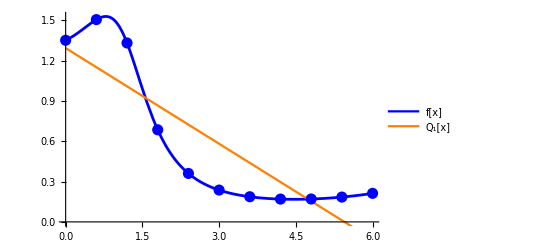

```mathematica
result=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,1}]];
polinomialResult=0;
m=1;
k=0;
While[k<=m,polinomialResult=polinomialResult+result[[k+1]]*x^k;k++];
Subscript[Q, 1]=polinomialResult;
Print["Q_1(x)=",Subscript[Q, 1]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Subscript[Q, 1],{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Q_1[x]"}]]
```

Q_2(x)=1.63798-0.619649 x+0.0636985 x^2

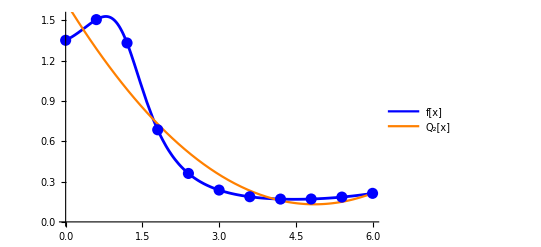

```mathematica
result=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,2}]];
polinomialResult=0;
m=2;
k=0;
While[k<=m,polinomialResult=polinomialResult+result[[k+1]]*x^k;k++];
Subscript[Q, 2]=polinomialResult;
Print["Q_2(x)=",Subscript[Q, 2]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Subscript[Q, 2],{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Q_2[x]"}]]
```

Q_3(x)=1.5429-0.367874 x-0.0463432 x^2+0.0122269 x^3

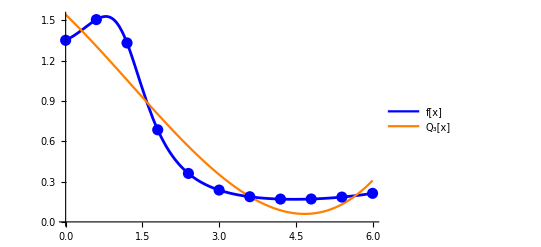

```mathematica
Subscript[Q, 3]=Fit[data,{1,x,x^2,x^3},x];
Print["Q_3(x)=",Subscript[Q, 3]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Subscript[Q, 3],{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Q_3[x]"}]]
```

Q_4(x)=1.39575+0.483684 x-0.755975 x^2+0.201462 x^3-0.0157696 x^4

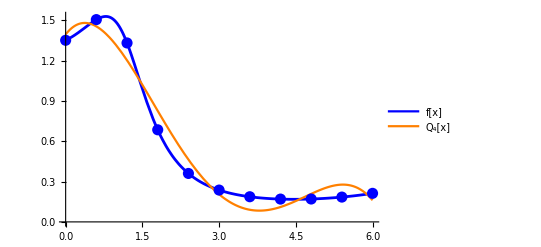

```mathematica
Subscript[Q, 4]=Fit[data,{1,x,x^2,x^3,x^4},x];
Print["Q_4(x)=",Subscript[Q, 4]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Blue,Thickness[0.005]}];
func2=Plot[Subscript[Q, 4],{x,A,B},PlotStyle->Orange];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Blue,Orange},{"f[x]","Q_4[x]"}]]
```

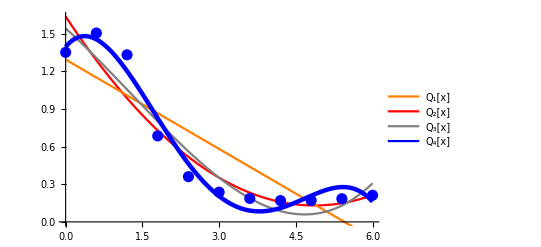

```mathematica
func1=Plot[Subscript[Q, 1],{x,A,B},PlotStyle->Orange];
func2=Plot[Subscript[Q, 2],{x,A,B},PlotStyle->Red];
func3=Plot[Subscript[Q, 3],{x,A,B},PlotStyle->Gray];
func4=Plot[Subscript[Q, 4],{x,A,B},PlotStyle->{Blue,Thickness[0.008]}];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func2,func1,func3,func4,dots],LineLegend[{Orange,Red,Gray,Blue},{"Q_1[x]","Q_2[x]","Q_3[x]","Q_4[x]"}]]
```